```mathematica
N[Solve[1-x1-x2/(1+x2) -x3/(1+x3) - x4/(1+x4)==0&&1-x2-x1/(1+x1) - x3/(1+x3)- x4/(1+x4)==0&&1-x3-x1/(1+x1) - x2/(1+x2)- x4/(1+x4)==0&&1-x3/(1+x3)-x1/(1+x1) - x2/(1+x2) - x4== 0, {x1, x2, x3, x4}]]
```

{{x1→-0.5,x2→1.,x3→1.,x4→1.},{x1→1.,x2→1.,x3→-0.5,x4→1.},{x1→1.,x2→1.,x3→1.,x4→-0.5},{x1→1.,x2→-0.5,x3→1.,x4→1.},{x1→-0.5-0.866025 ⅈ,x2→-0.5+0.866025 ⅈ,x3→-0.5-0.866025 ⅈ,x4→-0.5+0.866025 ⅈ},{x1→-0.5-0.866025 ⅈ,x2→-0.5+0.866025 ⅈ,x3→-0.5+0.866025 ⅈ,x4→-0.5-0.866025 ⅈ},{x1→-0.5-0.866025 ⅈ,x2→-0.5-0.866025 ⅈ,x3→-0.5+0.866025 ⅈ,x4→-0.5+0.866025 ⅈ},{x1→-0.5+0.866025 ⅈ,x2→-0.5-2.59808 ⅈ,x3→-0.5+0.866025 ⅈ,x4→-0.5+0.866025 ⅈ},{x1→-0.5+0.866025 ⅈ,x2→-0.5-0.866025 ⅈ,x3→-0.5+0.866025 ⅈ,x4→-0.5-0.866025 ⅈ},{x1→-0.5+0.866025 ⅈ,x2→-0.0540541+0.324324 ⅈ,x3→-0.5-0.866025 ⅈ,x4→-0.945946-0.324324 ⅈ},{x1→-3.30278,x2→-3.30278,x3→-3.30278,x4→-3.30278},{x1→0.302776,x2→0.302776,x3→0.302776,x4→0.302776}}

```mathematica
ContourPlot[{2+5*x1-x2/(1+x2)==0,2+5*x2-x1/(1+x1)==0 }, {x1, -5, 5}, {x2, -5, 5}];
```

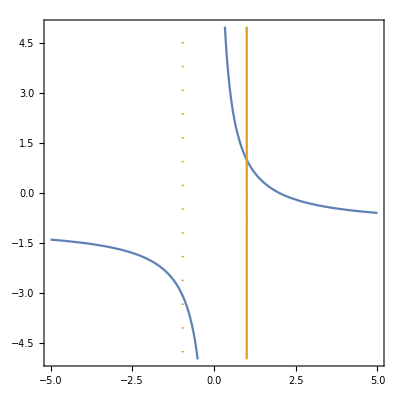

```mathematica
ContourPlot[{1-a11*x1+2*(a11-1)*x2/(1+x2)==0,1-(1-2*a11)*x2-4*a11*x1/(1+x1)==0}, {x1, -5, 5}, {x2, -5, 5}]
```

```mathematica
a11 = a11;
N[Solve[1-a11*x1+2*(a11-1)*x2/(1+x2)==0&&1-(1-2*a11)*x2-4*a11*x1/(1+x1)==0 {x1, x2}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→1.,x2→1.}}

```mathematica
FullSimplify[Solve[1-a11*x1+a12*x2/(1+x2)==0, {x2}][[1]][[1]][[2]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(-2.+x1)/(2.+2. a12-1. x1)
```

(-2.+x1)/(2.+2. a12-1. x1)

# Imposing tangency on a feasible planted equilibrium

```mathematica
Clear[a11];
eq1 = 1 - a11*x1 + a12*x2/(1 + x2) + a13*x3/(1+x3);
eq2 = 1 - a22*x2 - a21*x1/(1 + x1)+ a23*x3/(1+x3);eq3 = 1 - a33*x3 - a31*x1/(1 + x1)+ a32*x2/(1+x2);
```

```mathematica
constr1 = eq1/.x1-> 1/.x2->1 /.x3->1 ;
constr2 = eq2/.x1-> 1/.x2->1/.x3->1 ;
constr3 = eq3/.x1-> 1/.x2->1/.x3->1;
```

```mathematica
curve1 = Solve[eq1==0, x3][[1]][[1]][[2]];
curve2 = Solve[eq2==0, x3][[1]][[1]][[2]];
curve2 = Solve[eq2==0, x3][[1]][[1]][[2]];
```

(1+x1-a21 x1-a22 x2-a22 x1 x2)/(-1-a23-x1+a21 x1-a23 x1+a22 x2+a22 x1 x2)

```mathematica
derivative1 = D[curve1, x1]/.x1->1/.x2->1/.x3->1;
```

```mathematica
derivative2 = D[curve2, x1]/.x1->1/.x2->1/.x3->1;
```

```mathematica
Solve[constr1 == 0 && constr2 ==0&& derivative1==derivative2, {a12, a21, a22}]
```

{{a12→2 (-1+a11),a21→(8 a11)/(1+3 a11),a22→(1-a11)/(1+3 a11)}}

```mathematica
eq1constr = eq1/.a12->2 (-1+a11) +RandomReal[{-0.1, 0.1}]/.a21->(8 a11)/(1+3 a11)+RandomReal[{-0.1, 0.1}]/.a22->(1-a11)/(1+3 a11)+RandomReal[{-0.1, 0.1}];
eq2constr = eq2/.a12->2 (-1+a11)+RandomReal[{-0.1, 0.1}]/.a21->(8 a11)/(1+3 a11)+RandomReal[{-0.1, 0.1}]/.a22->(1-a11)/(1+3 a11)+RandomReal[{-0.1, 0.1}];
```

```mathematica
a11 = 0.5;
Solve[eq1constr==0&&eq2constr==0, {x1, x2}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→0.822035,x2→1.44715},{x1→1.99238,x2→0.00383864}}

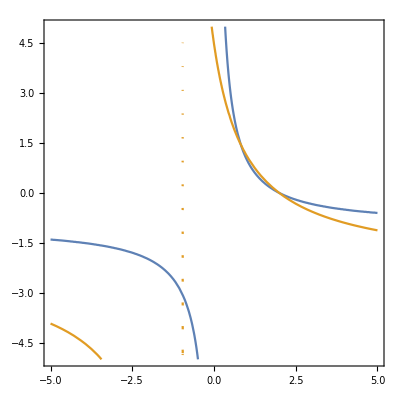

```mathematica
ContourPlot[{eq1constr, eq2constr}, {x1, -5, 5}, {x2, -5, 5}]
```

```mathematica
FullSimplify[n+1/2*n*(n-1)]
```

1/2 n (1+n)

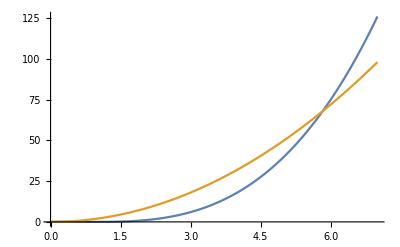

```mathematica
1/2 n (1+n)
Plot[{Binomial[n, 2]*(n-1), 2*n^2}, {n, 0, 7}]
```

## Putting glv with functional responses in polynomial form

```mathematica
Clear[a11]
eq1 = (1+x2)*(1+x3)*(r1 - a11*x1)+ x2*a12*(1+x3) + x3*a13*(1+x2);
MonomialList[eq1, {x1, x2, x3}]
```

{-a11 x1 x2 x3,-a11 x1 x2,-a11 x1 x3,-a11 x1,(a12+a13+r1) x2 x3,(a12+r1) x2,(a13+r1) x3,r1}

### Bidirectional mutualism in C-R

```mathematica
eq1 =(h2+x2)*(h3+x3)*(e1+x1)*(r1 - a11*x1) + a12*x2*(h3+x3)*(e1+x1) + a13*x3*(h2+x2)*(e1+x1)-(b31*x3 + b21*x2)*(h2+x2)*(h3+x3);
eq2 = (h1+x1)*(h3+x3)*(e2+x2)*(r2-a22*x2) + a21*x1*(h3+x3)*(e2+x2) + a23*x3*(h1+x1)*(e2+x2) - (b12*x1 + b32*x3)*(h1+x1)*(h3+x3);
eq3 = (h1+x1)*(h2+x2)*(e3+x3)*(r3-a33*x3) + a31*x1*(e3 + x3)*(h2+x2)+  a32*x2*(h1+x1)*(e3+x3)-(b13*x1+b32*x2)*(h1 + x1)*(h2+x2);
```

```mathematica
r1 = r2 =r3= 0.3;
a21 = a12 = 0.6;
a31=a13=0.6;
a32=a23=0.6;
q1 = q2 = 1;
b21 = b12 = 0.2;
b31 = b13 = 0.2;
b32 = b23 = 0.2;
c1 = c2 = 1;
a11=a22=a33 =0.01;
h1=h2=h3=0.3;
e1=e2=e3=0.3;
```

```mathematica
Solve[eq1==0&&eq2==0&&eq3==0, {x1, x2,x3}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x1→-0.3,x3→-0.3},{x1→-0.3,x2→-0.3},{x2→-0.3,x3→-0.3},{x1→-0.3,x2→-0.145023,x3→-0.3},{x1→0.375127,x2→-0.145023,x3→0.375127},{x1→-0.3,x2→-0.0819807,x3→-0.3},{x1→-0.0819807,x2→-0.0819807,x3→-0.0819807},{x1→-0.3,x2→-0.0626546,x3→-0.3},{x1→-0.0626546,x2→-0.0626546,x3→0.737623},{x1→0.737623,x2→-0.0626546,x3→-0.0626546},{x1→-0.3,x2→0.375127,x3→-0.3},{x1→-0.145023,x2→0.375127,x3→0.375127},{x1→0.375127,x2→0.375127,x3→-0.145023},{x1→-0.3,x2→0.737623,x3→-0.3},{x1→-0.0626546,x2→0.737623,x3→-0.0626546},{x1→-0.3,x2→1.2,x3→-0.3},{x1→-0.3,x2→27.3038,x3→-0.3},{x1→27.3038,x2→27.3038,x3→140.965},{x1→140.965,x2→27.3038,x3→27.3038},{x1→-0.3,x2→47.2428,x3→-0.3},{x1→121.784,x2→47.2428,x3→121.784},{x1→-0.3,x2→109.782,x3→-0.3},{x1→109.782,x2→109.782,x3→109.782},{x1→-0.3,x2→121.784,x3→-0.3},{x1→47.2428,x2→121.784,x3→121.784},{x1→121.784,x2→121.784,x3→47.2428},{x1→-0.3,x2→140.965,x3→-0.3},{x1→27.3038,x2→140.965,x3→27.3038}}

```mathematica
StreamPlot[{eq1, eq2},{x1, 0, 100}, {x2,0, 100}]
```

-Graphics-

### Mary’s suggestion

```mathematica
Clear[A]
f1=r-A*x1+B*(x2/(h+x2)+x3/(h+x3)+x4/(h+x4))-G/(k+x1)*(x2+x3+x4);
f2=r-A*x2+B*(x1/(h+x1)+x3/(h+x3)+x4/(h+x4))-G/(k+x2)*(x1+x3+x4);
f3=r-A*x3+B*(x2/(h+x2)+x1/(h+x1)+x4/(h+x4))-G/(k+x3)*(x2+x1+x4);
f4=r-A*x4+B*(x2/(h+x2)+x3/(h+x3)+x1/(h+x1))-G/(k+x4)*(x2+x3+x1);
```

```mathematica
h=k=1;
B=G=1;
A =1.01;
r=A;
```

```mathematica
soln = Solve[f1==0&&f2==0&&f3==0&&f4==0&&x1>0&&x2>0&&x3>0&&x4>0, {x1, x2, x3, x4}, Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→0.0220555,x2→0.0220555,x3→1.02112,x4→1.02112},{x1→0.0220555,x2→1.02112,x3→0.0220555,x4→1.02112},{x1→0.0220555,x2→1.02112,x3→1.02112,x4→0.0220555},{x1→0.759416,x2→0.759416,x3→1.1578,x4→1.1578},{x1→0.759416,x2→1.1578,x3→0.759416,x4→1.1578},{x1→0.759416,x2→1.1578,x3→1.1578,x4→0.759416},{x1→0.970229,x2→1.00954,x3→1.00954,x4→1.00954},{x1→1.,x2→1.,x3→1.,x4→1.},{x1→1.00954,x2→1.00954,x3→1.00954,x4→0.970229},{x1→1.00954,x2→0.970229,x3→1.00954,x4→1.00954},{x1→1.00954,x2→1.00954,x3→0.970229,x4→1.00954},{x1→1.02112,x2→0.0220555,x3→1.02112,x4→0.0220555},{x1→1.02112,x2→1.02112,x3→0.0220555,x4→0.0220555},{x1→1.02112,x2→0.0220555,x3→0.0220555,x4→1.02112},{x1→1.1578,x2→0.759416,x3→1.1578,x4→0.759416},{x1→1.1578,x2→1.1578,x3→0.759416,x4→0.759416},{x1→1.1578,x2→0.759416,x3→0.759416,x4→1.1578}}

```mathematica
J = {{D[f1, x1]/.{x1->1, x2->1, x3->1, x4->1},D[f1, x2]/.{x1->1, x2->1, x3->1, x4->1}, D[f1, x3]/.{x1->1, x2->1, x3->1, x4->1}, D[f1, x4]/.{x1->1, x2->1, x3->1, x4->1} }, {D[f2, x1]/.{x1->1, x2->1, x3->1, x4->1},D[f2, x2]/.{x1->1, x2->1, x3->1, x4->1}, D[f2, x3]/.{x1->1, x2->1, x3->1, x4->1}, D[f2, x4]/.{x1->1, x2->1, x3->1, x4->1}}, {D[f3, x1]/.{x1->1, x2->1, x3->1, x4->1},D[f3, x2]/.{x1->1, x2->1, x3->1, x4->1}, D[f3, x3]/.{x1->1, x2->1, x3->1, x4->1}, D[f3, x4]/.{x1->1, x2->1, x3->1, x4->1}}, {D[f4, x1]/.{x1->1, x2->1, x3->1, x4->1},D[f4, x2]/.{x1->1, x2->1, x3->1, x4->1}, D[f4, x3]/.{x1->1, x2->1, x3->1, x4->1}, D[f4, x4]/.{x1->1, x2->1, x3->1, x4->1}}}
```

{{-0.26,-1/4,-1/4,-1/4},{-1/4,-0.26,-1/4,-1/4},{-1/4,-1/4,-0.26,-1/4},{-1/4,-1/4,-1/4,-0.26}}

```mathematica
Eigenvalues[J]
```

{-1.01,-0.01,-0.01,-0.01}

```mathematica
{1-A,1-A,1-A,-A}
(*This means that the equilibrium (1,1,1,1) is stable when A > 1, and unstable when A < 1*)
```

### Beverton-Holt model

```mathematica
eq1 = a*x1^2/(1 + x1^2) - x1;
eq2 = b*x2^2/(1+x2^2) - x2;
eq3= c*x3^2/(1+x3^2) - x3;
a = 2.5;
b =c = a;
```

```mathematica
N[Solve[eq1==0&&eq2==0&&eq3==0&&x1>0&&x2>0&&x3>0,{x1, x2, x3}, Reals]]
```

{{x1→0.101021,x2→0.101021,x3→0.101021},{x1→9.89898,x2→0.101021,x3→0.101021},{x1→0.101021,x2→9.89898,x3→0.101021},{x1→9.89898,x2→9.89898,x3→0.101021},{x1→0.101021,x2→0.101021,x3→9.89898},{x1→9.89898,x2→0.101021,x3→9.89898},{x1→0.101021,x2→9.89898,x3→9.89898},{x1→9.89898,x2→9.89898,x3→9.89898}}

### Competitive Beverton-Holt model (as in Brett and Kulenović, 2014, p. 2)

```mathematica
eq1 = a*x1^2/(1 + x1^2 + c*x2) - x1;
eq2 = b*x2^2/(1+x2^2+ d*x1) - x2;
a = 2.5;
b = 2.2;
c=0.13;
d =0.09;
```

```mathematica
N[Solve[eq1==0&&eq2==0,{x1, x2}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→0.5,x2→0.},{x1→0.563425,x2→0.700886},{x1→0.642719,x2→1.49007},{x1→1.87702,x2→1.30265},{x1→1.91684,x2→0.90639},{x1→2.,x2→0.},{x1→0.,x2→0.},{x1→0.,x2→0.641742},{x1→0.,x2→1.55826}}

### Now with 3 species...

```mathematica
eq1 = a*x1^2/(1 + x1^2 + c*x2 + e*x3) - x1;
eq2 = b*x2^2/(1+x2^2+ d*x1 + f*x3) - x2;
eq3 = g*x3^2/(1+x3^2+ h*x1+ i*x2) - x3;
a = 2.5;
b = 2.2;
c=0.13;
d =0.09;
e = f = i = d;
g= 3;
```

```mathematica
N[Solve[eq1==0&&eq2==0&&eq3==0,{x1, x2, x3}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→0.5,x2→0.,x3→0.},{x1→0.562249-0.228235 ⅈ,x2→0.396579-1.82662 ⅈ,x3→1.00038-0.849742 ⅈ},{x1→0.562249+0.228235 ⅈ,x2→0.396579+1.82662 ⅈ,x3→1.00038+0.849742 ⅈ},{x1→0.563425,x2→0.700886,x3→0.},{x1→0.587371-0.0490886 ⅈ,x2→0.,x3→1.39813-0.722834 ⅈ},{x1→0.587371+0.0490886 ⅈ,x2→0.,x3→1.39813+0.722834 ⅈ},{x1→0.642719,x2→1.49007,x3→0.},{x1→0.792833-0.231243 ⅈ,x2→1.82806-2.45674 ⅈ,x3→1.88138+1.19937 ⅈ},{x1→0.792833+0.231243 ⅈ,x2→1.82806+2.45674 ⅈ,x3→1.88138-1.19937 ⅈ},{x1→1.64784-0.168309 ⅈ,x2→2.33943+2.39901 ⅈ,x3→1.42691-1.97723 ⅈ},{x1→1.64784+0.168309 ⅈ,x2→2.33943-2.39901 ⅈ,x3→1.42691+1.97723 ⅈ},{x1→1.87702,x2→1.30265,x3→0.},{x1→1.91263-0.144034 ⅈ,x2→0.,x3→1.60187+2.12091 ⅈ},{x1→1.91263+0.144034 ⅈ,x2→0.,x3→1.60187-2.12091 ⅈ},{x1→1.91684,x2→0.90639,x3→0.},{x1→1.99708-0.355685 ⅈ,x2→-0.164067+2.57713 ⅈ,x3→1.69133+2.18244 ⅈ},{x1→1.99708+0.355685 ⅈ,x2→-0.164067-2.57713 ⅈ,x3→1.69133-2.18244 ⅈ},{x1→2.,x2→0.,x3→0.},{x1→0.,x2→0.641742,x3→0.},{x1→0.,x2→1.03729-1.03195 ⅈ,x3→0.423661-0.0431441 ⅈ},{x1→0.,x2→1.03729+1.03195 ⅈ,x3→0.423661+0.0431441 ⅈ},{x1→0.,x2→1.16271-2.7428 ⅈ,x3→2.57634+0.114672 ⅈ},{x1→0.,x2→1.16271+2.7428 ⅈ,x3→2.57634-0.114672 ⅈ},{x1→0.,x2→1.55826,x3→0.},{x1→0.,x2→0.,x3→0.},{x1→0.,x2→0.,x3→0.381966},{x1→0.,x2→0.,x3→2.61803}}